# Constructing protein surfaces

Yury Polyachenko

MIPT

Motivation: Biology, and especially computational molecular biology has been growing exponentially for the last decade and perhaps even more. E.g. the problem of docking always has been crucial for the drug design. But the usual molecular dynamics approach to the problem often is too computationally expensive. It is even more relevant it the context of the ongoing COVID pandemic as we want to analyse enormous databases of bio-molecules in very short periods of time. One new approach to the problem suggests [1-3] using only surfaces of molecules because surfaces are what one would expect to impact docking mostly but they their analysis require way less computations.
Goal: To create a WL package for construction and visualization of protein surfaces. This can be the 1st step on the way to implementing auto-docking tools such as [1].
Results: The package implements the 2 main functions corresponding to the 2 types of surfaces. Tools necessary for sound work with proteins are also provided. All the code is packed to a package. The package has an installation function which runs automatically on its import.
Methods: More specifically the constructions of solvent accessible surface [4] (SAS) and of solvent excluded surface [4] (SES) are implemented using MSMS program [4]. SAS of a protein is a surface formed by points which a center of a probe solvent molecule rolling over the protein can occupy. SES of a molecule is the inner boundary of the union of all possible probes that do not overlap with the protein. PDB files often do not have hydrogen atoms in them so one may want to protonate a protein before running surface analysis to gain a surface closer to the one acting in the real world. Often the impact of protonation on a surface is minimal, but it may not always be the case. A function for protonation is implemented using the Reduce program [5].

## Wolfram Community Post (material for blog post)

<describe ideas or arguments in a clear narrative format. explain how the topic/idea is studied and how it is implemented in the Wolfram language codes>

<one-line text, explaining the code only> Plot several functions with a legend:

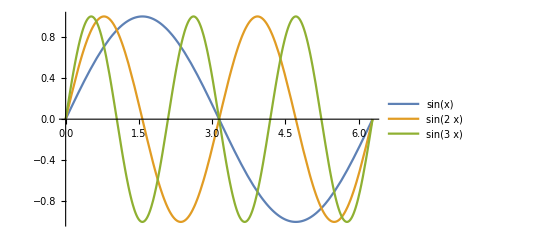

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotLegends->"Expressions"]
```

## Complete project work

<describe ideas or arguments in a clear narrative format. explain how the topic/idea is studied and how it is implemented in the Wolfram language codes>

<one-line text, explaining the code only> Plot several functions with a legend:

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotLegends->"Expressions"]
```

-Graphics-

## Keywords

<Keyword1>

Keyword2

....

## Acknowledgment

Mentor: <Mentor first name and last name>

<text>

## References